```mathematica
ClearAll["Global`*"];
Clear[alpha,s,mme,Emu,coseMinLA,cosmMinLA,coseMinCM,EeMinLA,GevToBarn];
<<"C:\Users\PC\OneDrive\Documents\Wolfram Mathematica\NumericalThesis\\N-point.txt";(*import N-point function*)
<<"C:\Users\PC\OneDrive\Documents\Wolfram Mathematica\NumericalThesis\Check\\Box_u.txt";(*import squared NLO amplitude*)
<<"C:\Users\PC\OneDrive\Documents\Wolfram Mathematica\NumericalThesis\\Soft_photon.txt";(*import soft-photon term*)
(*<<X`;(*import package X to calcualate Feynman Functions*)
$UserBaseDirectory;(*find Mathematica application to import package*)*)
(*choose precision digits*)
np=100;
eps:=10^-33;
(*to micro-barn*)
GevToBarn=SetPrecision[0.3893793721*10^3,np];
alpha=SetPrecision[1/137.03599907430637,np];
pi=Pi;
e=SetPrecision[Sqrt[alpha*4*Pi],np];
Emu = 150;(*GeV*)
mme=SetPrecision[0.510998928*10^-3,np];(*GeV*)
EeCM:=Sqrt[mme^2+ppeCM^2];
mmu=SetPrecision[105.6583715*10^-3,np];(*GeV*)
EmuCM:=Sqrt[mmu^2+ppeCM^2];
deltaE:=10^-4*Sqrt[s[cthe]]/2;
coseMinLA=Cos[1/10];
cosmMinLA=coseMinLA;
coseMinCM = SetPrecision[0.9,np];
EeMinLA=SetPrecision[0.2,np];
s[cthe_]:=mme^2+mmu^2+2*mme*Emu;
rs[cthe_]:=Sqrt[s[cthe]];
t[cthe_]:=(mme^2+mmu^2-1/2*(((mmu^2-mme^2)^2)/s[cthe]+s[cthe]))*(1-cthe);
u[cthe_]:=2*(mmu^2+mme^2)-s[cthe]-(mme^2+mmu^2-1/2*(((mmu^2-mme^2)^2)/s[cthe]+s[cthe]))*(1-cthe);
ppeCM:= Sqrt[(mme^2+mmu^2-1/2*(((mmu^2-mme^2)^2)/s[cthe]+s[cthe]))/-2];
dsigmaVir[cthe_]:=NLOMS[cthe]/(64*Pi^2*s[cthe]);
 dsigmaO[cthe_]:= (2*alpha^2)/(t[cthe]^2*s[cthe])*(s[cthe]^2/4+u[cthe]^2/4+(mmu^2+mme^2)*t[cthe]-((mmu^2+mme^2)^2)/2);
dsigmaNLO[cthe_]:= dsigmaVir[cthe]+dsigmaSoft[cthe]+dsigmaO[cthe];
Table[Re[2*Pi*GevToBarn*(dsigmaSoft[cthe]+dsigmaVir[cthe])/.{s->s[cthe],t->t[cthe],u->u[cthe],nu->1,Lambda->1}],{cthe,{-0.9,-0.5,-0.1,0,0.1,0.5,0.9}}]//MatrixForm
```

((((-0.164993)))
(((-0.350553)))
(((-0.776518)))
(((-0.977404753232300711223522880710204771654298561200786093868843250334334748668151972168982)))
(((-1.25258)))
(((-4.54102)))
(((-98.4482))))

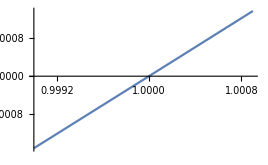

```mathematica
Plot[s[0.5]*x^2+(mme^2-mmu^2-s[0.5])*x+mmu^2,{x,0.999,1.0009}]
```

```mathematica
C0b[cthe_,tba_,m1_,m2_]:=(-xt[cthe,tba,m1,m2])/(m1*m2*(1-xt[cthe,tba,m1,m2]^2))*Log[xt[cthe,tba,m1,m2]]*Log[Lambda^2/(m1*m2)]+xt[cthe,tba,m1,m2]/(2*m1*m2*(1-xt[cthe,tba,m1,m2]^2))*((Log[(Z1[cthe,tba,m1,m2]-1)/Z1[cthe,tba,m1,m2]]-Log[(Z2[cthe,tba,m1,m2]-1)/Z2[cthe,tba,m1,m2]])*(Log[(tba[cthe]+I*eps)/(m1*m2)])+Integrate[(1/(x-Z1[cthe,tba,m1,m2])-1/(x-Z2[cthe,tba,m1,m2]))*(Log[x-Z1[cthe,tba,m1,m2]]+Log[x-Z2[cthe,tba,m1,m2]]),{x,0,1}]);
C0a[cthe_,tba_,m1_,m2_]:=(-xt[cthe,tba,m1,m2])/(m1*m2*(1-xt[cthe,tba,m1,m2]^2))*Log[xt[cthe,tba,m1,m2]]*Log[Lambda^2/(m1*m2)]+xt[cthe,tba,m1,m2]/(2*m1*m2*(1-xt[cthe,tba,m1,m2]^2))*(2*Log[xt[cthe,tba,m1,m2]]*(Log[(tba[cthe]+I*eps)/(m1*m2)]+Log[Z1[cthe,tba,m1,m2]-Z2[cthe,tba,m1,m2]]+Log[Z2[cthe,tba,m1,m2]-Z1[cthe,tba,m1,m2]])-PolyLog[2,Z2[cthe,tba,m1,m2]/Z1[cthe,tba,m1,m2]]+PolyLog[2,(1-Z2[cthe,tba,m1,m2])/(1-Z1[cthe,tba,m1,m2])]-PolyLog[2,(1-Z1[cthe,tba,m1,m2])/(1-Z2[cthe,tba,m1,m2])]+PolyLog[2,Z1[cthe,tba,m1,m2]/Z2[cthe,tba,m1,m2]]);
```

```mathematica
Table[SetPrecision[C0b[cthe,s,mme,mmu]/.Lambda->1,np],{cthe,{-0.9,-0.5,0.5,0.9}}]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{-440.7826774095261585122312560493655154800745442536422121024461164860320165132987078895264078597275535+39.8726189500095903763880639966269667177973749601595769874458430007529219729946628276776966883301103 ⅈ,-440.7826774095261585122312560493655154800745442536422121024461164860320165132987078895264078597275535+39.8726189500095903763880639966269667177973749601595769874458430007529219729946628276776966883301103 ⅈ,-440.7826774095261585122312560493655154800745442536422121024461164860320165132987078895264078597275535+39.8726189500095903763880639966269667177973749601595769874458430007529219729946628276776966883301103 ⅈ,-440.7826774095261585122312560493655154800745442536422121024461164860320165132987078895264078597275535+39.8726189500095903763880639966269667177973749601595769874458430007529219729946628276776966883301103 ⅈ}

```mathematica
Table[SetPrecision[C0[cthe,s,mme,mmu]/.Lambda->1,np],{cthe,{-0.9,-0.5,0.5,0.9}}]
```

{-440.7826774095261585122312560493655154800745442536422121024461164860320165132987078895264078593392204+39.8726189500095903763880639966269667177973749601595769874458430007529219729946628276776966883301103 ⅈ,-440.7826774095261585122312560493655154800745442536422121024461164860320165132987078895264078593392204+39.8726189500095903763880639966269667177973749601595769874458430007529219729946628276776966883301103 ⅈ,-440.7826774095261585122312560493655154800745442536422121024461164860320165132987078895264078593392204+39.8726189500095903763880639966269667177973749601595769874458430007529219729946628276776966883301103 ⅈ,-440.7826774095261585122312560493655154800745442536422121024461164860320165132987078895264078593392204+39.8726189500095903763880639966269667177973749601595769874458430007529219729946628276776966883301103 ⅈ}

```mathematica
Table[SetPrecision[Re[2*Pi*GevToBarn*(dsigmaSoft[cthe])/.{s->s[cthe],t->t[cthe],u->u[cthe],nu->1,Lambda->1}],np],{cthe,{-0.9,-0.5,-0.1,0,0.1,0.5,0.9}}]//MatrixForm
```

((((-0.274018485715011361758541852395865134894847869873046875)))
(((-0.55687994739764457019504106938256882131099700927734375)))
(((-1.2568132404822096592766911271610297262668609619140625)))
(((-1.594164651660385078507510240125775790071883231537389523336748618164049003404724003411752607472156941)))
(((-2.061493165855819764686884809634648263454437255859375)))
(((-7.9067165148562974508195111411623656749725341796875)))
(((-210.0732710305745740697602741420269012451171875))))

```mathematica
T[cthe_,tba_,m1_,m2_]:=Integrate[(1/(x-Z1[cthe,tba,m1,m2])-1/(x-Z2[cthe,tba,m1,m2])),{x,0,1}];
P[cthe_,tba_,m1_,m2_]:=Log[(Z1[cthe,tba,m1,m2]-1)/Z1[cthe,tba,m1,m2]]-Log[(Z2[cthe,tba,m1,m2]-1)/Z2[cthe,tba,m1,m2]];
```

```mathematica
2*Log[xt[-0.9,s,mme,mmu]]
T[-0.9,s,mme,mmu]
P[-0.9,s,mme,mmu]
```

-15.90265330124847167534390481803083312627434088498605025098616526047982235114757114690891627108201854+6.28318530717958647692528676655899272204931682348003951043219488682968222711677220370134897501497436 ⅈ

-15.90265330124847167534390481803083312627434088498605025098616526047982235114757114690891627108+6.283185307179586476925286766558992722049316823480039510432194886829682227116772203701348975015 ⅈ

-15.90265330124847167534390481803083312627434088498605025098616526047982235114757114690891627108+6.283185307179586476925286766558992722049316823480039510432194886829682227116772203701348975015 ⅈ

```mathematica
xt[-0.9,s,mme,mmu]^2
```

1.2404104708382380208764224978064080866835430007686772498782619482143768559414054209086873329065646×10^-7-1.6182822971426447633482154014453579846481811132627593575613468211578008023727408420789714345920424×10^-39 ⅈ

```mathematica
M[cthe_,x_,tba_,m1_,m2_]:=Log[((tba[cthe]+I*eps)*x^2+(m1^2-m2^2-(tba[cthe]+I*eps))*x+m2^2)/(m1*m2)];
H[cthe_,x_,tba_,m1_,m2_]:=Log[(x-Z1[cthe,tba,m1,m2])*(x-Z2[cthe,tba,m1,m2])]+Log[(tba[cthe]+I*eps)/(m1*m2)];
L[cthe_,x_,tba_,m1_,m2_]:=Log[(x-Z1[cthe,tba,m1,m2])]+Log[(x-Z2[cthe,tba,m1,m2])]+Log[(tba[cthe]+I*eps)/(m1*m2)];
K[cthe_,x_,tba_,m1_,m2_]:=(x-Z1[cthe,tba,m1,m2])*(x-Z2[cthe,tba,m1,m2]);
J[cthe_,x_,tba_,m1_,m2_]:=((tba[cthe]+I*eps)*x^2+(m1^2-m2^2-(tba[cthe]+I*eps))*x+m2^2)/(tba[cthe]+I*eps)
```

```mathematica
M[0.9,0.1,s,mme,mmu]
H[0.9,0.1,s,mme,mmu]
L[0.9,0.1,s,mme,mmu]
K[-0.9,0.1,s,mme,mmu]
J[-0.9,0.1,s,mme,mmu]
```

4.478-3.14159 ⅈ

4.478-3.14159 ⅈ

4.478-3.14159 ⅈ

-0.0289084-3.7146×10^-34 ⅈ

-0.0289084-3.7146×10^-34 ⅈ